# Modified Slavnov-Taylor Identity: Gluon Two-Point Function

This notebook derives the modified Slavnov-Taylor Identity (mSTI) of the gluon two-point function in SU(3) Yang-Mills theory.
The mSTIs encode BRST symmetry in the presence of an infrared momentum cutoff. At scale k, the master equation reads:
                δΓ/δQ^a · δΓ/δΦ^a =  R^ab G_bc (Γ^c)_(Q^a)
For k → 0 the RHS vanishes and the ordinary STIs are recovered.

## Setup

## Load FunKit

```mathematica
Get["FunKit`"]
```

Welcome to  █▀ ▐▄█ █▚▌ ▐◀ █ ▀█▀
Author: Franz Richard Sattler
Version: 0.1.2
Year: 2025
For more information and a brief introduction to the package, call FInfo[].
To run the testing suite, you can call  FTest[].

## Field Space

The field space includes the physical Yang-Mills fields (gluon A, ghosts c and cb) plus the BRST source fields (QA, Qcb, Qc).
  - QA is commuting
  - Qcb and Qc are grassmann

```mathematica
fields = <|
"Commuting" -> {A[p, {v, c}]},
"Grassmann" -> {{cb[p, {c}], c[p, {c}]}},
"CommutingSource"->{Qcb[p], Qc[p]},
"GrassmannSource"->{QA[p, {v, c}]}
|>;
```

## Truncations

```mathematica
truncation = <|
GammaN -> {
{A, A}, {cb, c},
{A, A, A}, {A, A, A, A}, {A, cb, c},
{A, Qcb}, {c, QA}, {A, c, QA}, {c, c, Qc}
},
Propagator -> {{A, A}, {cb, c}},
R -> {{A, A}, {cb, c}}
|>;
```

## Build Setups

```mathematica
Setup=<|
"FieldSpace" -> fields,
"Truncation" -> truncation
|>;
FSetGlobalSetup[Setup];

FSetTexStyles[
QA->"{Q^{A}}",
Qc->"{Q^{c}}",
cb->"\\bar{c}",
Qcb->"{Q^{\\bar{c}}}"
];
```

## mSTI Master Equation

## LHS

The LHS of the mSTI is the product of BRST-source derivatives and field-space derivatives of the effective action, summed over all BRST source channels:

```mathematica
mSTILHS = Module[{idx},
idx = Symbol @ SymbolName @ Unique["a"];
FEx[
FTerm[1,  GammaN[{QA},{idx}], GammaN[{A},{-idx}]],
FTerm[1,  GammaN[{Qcb},{idx}], GammaN[{cb},{-idx}]],
FTerm[1, GammaN[{Qc},{idx}], GammaN[{c},{-idx}]]
]
];
```

## RHS: One-Loop with Regulator Insertion

We pre-expand over the BRST source channels (Q^A and Q^c) but keep R and Propagator as AnyField. This allows the truncation machinery to explore all possible field routes through the loop, which is essential for generating the ghost triangle diagram (which requires both G^AA and G_ccb in the same loop).

The Q^cb channel is absent because the BRST transform of cb is proportional to the divergence of A (gauge-fixing), and the corresponding one-loop BRST vertex does not contribute at this truncation level.

```mathematica
mSTIRHS = Module[{a, b, c1},
a  = Symbol @ SymbolName @ Unique["a"];
b  = Symbol @ SymbolName @ Unique["a"];
c1 = Symbol @ SymbolName @ Unique["a"];
FEx[
(* Channel Q^A *)
FTerm[1,
R[{AnyField, AnyField}, {-a, -b}],
Propagator[{AnyField, AnyField}, {b, c1}],
GammaN[{AnyField, QA}, {-c1, a}]
],
(* Channel Q^c *)
FTerm[1,
R[{AnyField, AnyField}, {-a, -b}],
Propagator[{AnyField, AnyField}, {b, c1}],
GammaN[{AnyField, Qc}, {-c1, a}]
],
(* Channel Q^cb *)
FTerm[1,
R[{AnyField, AnyField}, {-a, -b}],
Propagator[{AnyField, AnyField}, {b, c1}],
GammaN[{AnyField, Qcb}, {-c1, a}]
]
]
];
```

## Derive the Gluon Two-Point mSTI

## LHS Derivation

We differentiate the LHS with respect to {A, c} and truncate.


-Graphics-+-Graphics--Graphics-

-Graphics-

```mathematica
mSTILHSAc=FTakeDerivatives[mSTILHS,{A[i1],c[i2]}]//FTruncate;
mSTILHSAc//FPlot//FPrint;
```

## RHS Derivation

We differentiate the RHS with respect to {A, c} and truncate.

-Graphics-+-Graphics-+-Graphics-+-Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

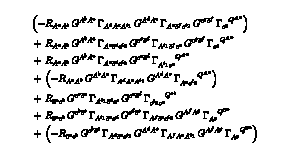

```mathematica
mSTIRHSAc=FTakeDerivatives[mSTIRHS,{A[i1],c[i2]}]//FTruncate;
mSTIRHSAc//FPlot//FPrint;
```